```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
NotebookEvaluate[StringJoin[ToString[NotebookDirectory[]],"library.nb"]];
```

```mathematica
net={n1,{n2,{n3},{n4,{n5},{n6,{n7},{n8,{n9},{n10,{n11,{n12},{n13}},{n14,{n15},{n16,{n17},{n18,{n19,{n20},{n21}},{n22,{n23},{n24}}}}}}}}}}};
```

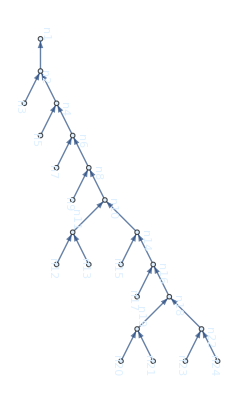

```mathematica
RepresentNetwork[net,90,True,0.001]
```

```mathematica
VerifyNetwork[net]
```

The network is a list.

The network is not empty.

The network does not contain repeated nodes.

The source nodes are:

{{n3},{n5},{n7},{n9},{n12},{n13},{n15},{n17},{n20},{n21},{n23},{n24}}

Checking internal nodes...

Checks concluded! Verification of the hydrographic network is complete!

```mathematica
InitializeNetwork[net,P]
```

Initializing the network...

Please insert the lengths of branches starting by the upstream node and
ending with the downstream node.

If the values of the lengths appear, the network
has been already initialized.
The lengths inserted are:

{L[n2,n1],L[n3,n2],L[n4,n2],L[n5,n4],L[n6,n4],L[n7,n6],L[n8,n6],L[n9,n8],L[n10,n8],L[n11,n10],L[n12,n11],L[n13,n11],L[n14,n10],L[n15,n14],L[n16,n14],L[n17,n16],L[n18,n16],L[n19,n18],L[n20,n19],L[n21,n19],L[n22,n18],L[n23,n22],L[n24,n22]}

The remaining lengths are:

It is necessary to define the P.

If the values of P appear,
the network has been already initialized, otherwise P values to define are:

{P[n2,n1],P[n3,n2],P[n4,n2],P[n5,n4],P[n6,n4],P[n7,n6],P[n8,n6],P[n9,n8],P[n10,n8],P[n11,n10],P[n12,n11],P[n13,n11],P[n14,n10],P[n15,n14],P[n16,n14],P[n17,n16],P[n18,n16],P[n19,n18],P[n20,n19],P[n21,n19],P[n22,n18],P[n23,n22],P[n24,n22]}

The network has the subsequent number of nodes: 24.

It is possible to compute the new nested network

```mathematica
flatnet=Flatten[net];
Do[(rho[flatnet[[i]],0]=0;),{i,1,Length[flatnet]}];
rho[n5,0]=5;
rho[n15,0]=4;
rho[n21,0]=6;
```

```mathematica
P[n2,n1]=0.69;
P[n3,n2]=0.82;
P[n4,n2]=0.94;
P[n5,n4]=0.30;
P[n6,n4]=0.67;
P[n7,n6]=0.84;
P[n8,n6]=0.47;
P[n9,n8]=0.68;
P[n10,n8]=0.97;
P[n11,n10]=0.71;
P[n12,n11]=0.79;
P[n13,n11]=0.39;
P[n14,n10]=0.56;
P[n15,n14]=0.32;
P[n16,n14]=0.71;
P[n17,n16]=0.83;
P[n18,n16]=0.67;
P[n19,n18]=0.83;
P[n20,n19]=0.81;
P[n21,n19]=0.59;
P[n22,n18]=0.41;
P[n23,n22]=0.81;
P[n24,n22]=0.31;
```

```mathematica
Do[(rho[Flatten[net][[i]],0]=0;),{i,1,Length[Flatten[net]]}]
```

```mathematica
t1=1;
tn=15;
```

```mathematica
rho[n5,0]=5;rho[n21,0]=6;rho[tn,0]=4;
```

```mathematica
ComputeMasterEquations[net,rho,t1,tn,P];
```

Thenecessarytimeis0.089323seconds.

```mathematica
results={Table[{i,rho[n1,i]},{i,0,tn}],Table[{i,rho[n4,i]},{i,0,tn}],Table[{i,rho[n6,i]},{i,0,tn}],Table[{i,rho[n10,i]},{i,0,tn}],Table[{i,rho[n15,i]},{i,0,tn}],Table[{i,rho[n18,i]},{i,0,tn}],Table[{i,rho[n21,i]},{i,0,tn}]};
```

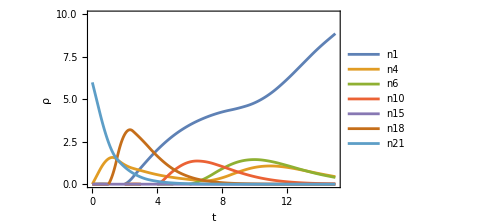

```mathematica
ListLinePlot[results,InterpolationOrder->2,PlotRange->{{0,15},{0,10}},FrameLabel->{"t","ρ"},PlotLegends->Placed[{"n1","n4","n6","n10","n15","n18","n21"},Top],Frame->True,ImageSize->Medium]
```

```mathematica
NotebookSave[];
```